# Choropleths for 2019-nCov

```mathematica
ds=ResourceData["Epidemic Data for Novel Coronavirus 2019-nCoV from Wuhan, China"];
```

```mathematica
ds[1]
```

```mathematica
ds[Select[#Country["Name"]==="China"||#Country["Name"]==="Taiwan"&],{"AdministrativeDivision","ConfirmedCases"}]
```

```mathematica
list=Normal[ds[Select[#Country["Name"]==="China"||#Country["Name"]==="Taiwan"&],(#AdministrativeDivision/.{Entity["AdministrativeDivision",{"Taiwan","Taiwan"}]->Entity["Country","Taiwan"]})->#ConfirmedCases["LastValue"]&]]
```

{Hubei, China→16678,Zhejiang, China→895,Guangdong, China→870,Henan, China→764,Hunan, China→661,Jiangxi, China→548,Anhui, China→530,Chongqing, China→366,Jiangsu, China→341,Sichuan, China→301,Shandong, China→298,Shanghai, China→233,Beijing, China→228,Fujian, China→194,Heilongjiang, China→190,Shanxi, China→165,Guangxi, China→150,Hebei, China→135,Yunnan, China→122,Hainan, China→91,Shaanxi, China→81,Liaoning, China→81,Tianjin, China→67,Guizhou, China→64,Gansu, China→57,Jilin, China→54,Neimenggu, China→42,Ningxia, China→34,Xinjiang, China→32,Qinghai, China→17,Taiwan→11,Xizang, China→1}

```mathematica
Log[1+16678]/10.
```

0.972191

```mathematica
i2c[i_]:=Blend[{White,Purple},Log[1+i]/10.]
```

```mathematica
Manipulate[Graphics[{Blend[{White,Purple},p],Disk[]}],{p,0,1}]
```

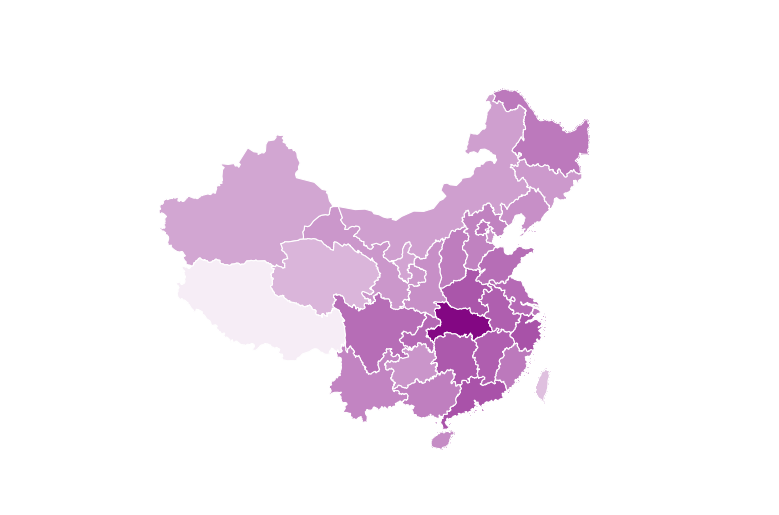

```mathematica
GeoGraphics[Map[
{GeoStyling[{EdgeForm[White],FaceForm[i2c[Last[#]]]}],First[#]["Polygon"]}&,
list],GeoBackground->None]
```

```mathematica
makeplot[list_,date_]:=GeoGraphics[
Map[{GeoStyling[{EdgeForm[{AbsoluteThickness[1],White}],FaceForm[i2c[Last[#]]]}],Tooltip[First[#]["Polygon"],Style[Column[{First[#]["Name"],Last[#]}],24]]}&,list],GeoProjection->"Orthographic",GeoRange->Automatic,GeoCenter->Entity["Country","China"],ImageSize->1000,GeoBackground->None,Epilog->Text[Style["2019-nCov\nconfirmed cases\n"<>DateString[date],16],Scaled[{.25,.25}]]]
```

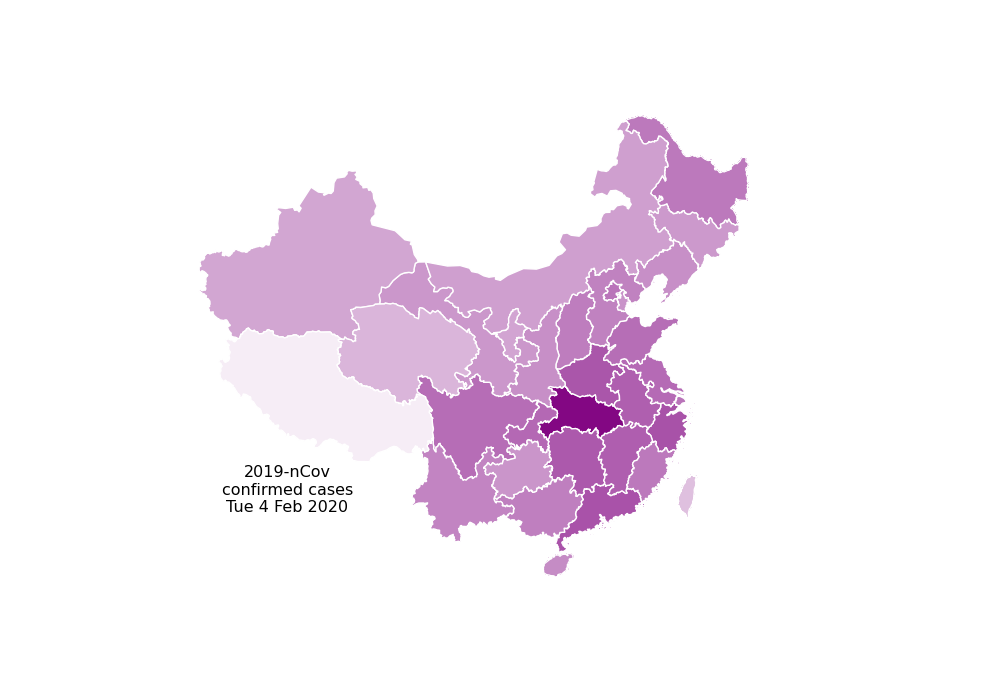

```mathematica
makeplot[list,DateObject[{2020,2,4}]]
```

```mathematica
DateString[Today]
```

Tue 4 Feb 2020

```mathematica
Export["D:\\git\\wolfram-coronavirus\\images\\confirmed-cases-02042020.png",ImageCrop[Rasterize[Out[86],"Image",ImageSize->1000]]]
```

D:\git\wolfram-coronavirus\images\confirmed-cases-02042020.png